## functions and seismological networks in OK

```mathematica
AroundPosition[ EqC_,WPos_,Rad_]:=Module[{distFrom,kselect},
distFrom=QuantityMagnitude@GeoDistance[WPos, #]&/@EqC[[2;;,{3,4}]]; (* in km*)
kselect=Position[distFrom,_?(#<=Rad &)]//Flatten;
Join[{EqC[[1]]},EqC[[kselect+1,;;]] ](* always keep the first row descriptor in data *)
];
AboveMagnitude[EqC_,Mag_]:= Module[{kselect},
kselect= Position[EqC[[2;;,12]],_?(#>Mag &)]//Flatten;
Join[{EqC[[1]]},EqC[[1+kselect,;;]] ](* always keep the first row descriptor in data *)
]
```

```mathematica
(* STATIONS OF THE OK NETWORK *)
OKNetwork={{Station Code, Station Name, Latitude ,Longitude, Data Center(s)},
{AMES, "Ames,Oklahoma,USA", 36.335587,-98.192787, IRISDMC},
{BCOK, "Bluff Creek,North Oklahoma City,Oklahoma" ,35.656731,-97.609276 ,IRISDMC},
{BLOK, "Blackwell,Oklahoma,USA", 36.760616,-97.215027, IRISDMC},
{BLUF, "Edmond,Oklahoma,USA", 35.656658,-97.609329 ,IRISDMC},
{CCOK, "Cow Creek,Oklahoma,USA", 35.356842,-97.656075, IRISDMC},
{CHOK, "Chandler,Oklahoma,USA", 35.561127,-97.061302, IRISDMC},
{CROK, "Carrier,Oklahoma,USA", 36.504738,-97.983353, IRISDMC},
{CSTR, "Hydro,Oklahoma,USA", 35.645557,-98.688889, IRISDMC},
{DEOK, "Depew,Oklahoma,USA", 35.842651,-96.49826, IRISDMC},
{ELIS, "Ellis County,Oklahoma ",36.065254,-99.418045 ,IRISDMC},
{FNO, "Franklin,Norman,Oklahoma,USA" ,35.257381,-97.401154, IRISDMC},
{FRLY, "Farley,Oklahoma,USA", 35.415272,-97.451767, IRISDMC},
{GC02, "Grant County #2,Oklahoma,USA" ,36.851501,-97.859589, IRISDMC},
{GORE, "Gore Oklahoma",36.785633,-97.94706 ,IRISDMC},
{HTCH, "Hitchcock,Oklahoma,USA", 36.017059,-98.332695, IRISDMC},
{KAY1, "Blackwell Oklahoma", 36.762653,-97.212219, IRISDMC},
{KNG1, "Kingfisher County,Oklahoma",36.132309,-97.69548, IRISDMC},
{LOOK, "Love County,Oklahoma,USA", 33.992428,-97.179993, IRISDMC},
{LOV1, "Marsden,Oklahoma", 34.059341,-97.240837, IRISDMC},
{LOV3, "Lake Murray,OK", 34.012989,-97.084778, IRISDMC},
{LOV5, "Oswalt Rd,Marietta Oklahoma", 34.0247,-97.158554, IRISDMC},
{LOV6, "Crinerville Rd,Ardmore Oklahoma", 34.09745,-97.211716 ,IRISDMC},
{LOV7, "Love County,Oklahoma", 33.999249,-97.26815 ,IRISDMC},
{MOOR, "Moore,Oklahoma,USA", 35.341793,-97.659218, IRISDMC},
{NOKA, "Waynoka,Oklahoma,USA", 36.634682,-98.931931 ,IRISDMC},
{OKCFA, "Farley,Oklahoma City,OK", 35.41531,-97.451767, IRISDMC},
{OKCSW, "Sweetheart,Southeast Oklahoma City,Oklahoma" ,35.405521,-97.438004, IRISDMC},
{QUOK, "Quay,Oklahoma,USA",36.171398,-96.708 ,IRISDMC},
{RLOK, "Rose Outlook,Oklahoma,USA", 36.167553,-95.026794, IRISDMC},
{SMO, "Science Museum,Oklahoma,USA", 35.523144,-97.474663, IRISDMC},
{SWND, "Oklahoma City,Oklahoma,USA", 35.405491,-97.437988 ,IRISDMC},
{U32A, "Winter Ranch,Mooreland,Oklahoma,USA", 36.379501,-99.001404 ,IRISDMC},
{W35A, "Tecumseh,Oklahoma,USA", 35.15274,-96.874527 ,IRISDMC},
{X34A, "Smith Ranch,Marlow,Oklahoma,USA", 34.601021,-97.832558, IRISDMC},
{X37A, "Clayton,Oklahoma,USA" ,34.589199,-95.3713, IRISDMC}};
```

```mathematica
(* STATIONS OF THE GS  OK NETWORK *)
GSOKNetwork={{Station Code, Station Name, Latitude ,Longitude, Data Center(s)},
{OK001," Jones High School,Jones,OK", 35.561089,-97.28949 ,IRISDMC},
{OK002," Wilshire Blvd and Luther Rd.,Jones,OK", 35.549339,-97.196632 ,IRISDMC},
{OK003," Hefner Rd,Jones,OK", 35.580101,-97.33786, IRISDMC},
{OK004," Oklahoma Science Museum,Oklahoma City,OK,USA", 35.523239,-97.474747 ,IRISDMC},
{OK005," Luther Middle School,Luther,OK", 35.654861,-97.191101 ,IRISDMC},
{OK006," Choctaw High School,Choctaw,OK", 35.477982,-97.278709 ,IRISDMC},
{OK007," Harrah City Hall,Harrah,OK", 35.487679,-97.161148, IRISDMC},
{OK008," City Hall,Spencer,OK", 35.507099,-97.383781 ,IRISDMC},
{OK009," Oakdale Elementary School,Edmond,OK", 35.58131,-97.42292, IRISDMC},
{OK010," NE 150th St,near Luther,OK", 35.624821,-97.224113 ,IRISDMC},
{OK011," Temporary Deployment,Prague,OK", 35.485229,-96.685783 ,IRISDMC},
{OK012," Temporary Deployment,Prague,OK", 35.503311,-96.900757, IRISDMC},
{OK020," N3440 Rd,Meeker,Oklahoma,USA", 35.537525,-96.876846 ,IRISDMC},
{OK021," N3530 Rd,Sparks,Oklahoma,USA", 35.602299,-96.718361, IRISDMC},
{OK022," S3560 Rd,Prague,Oklahoma,USA", 35.536839,-96.664909 ,IRISDMC},
{OK023," 25001 E Waterloo Rd,OK,USA", 35.724697,-97.162308, IRISDMC},
{OK024," West corner of E0890 Rd,OK,USA", 35.725056,-97.057915, IRISDMC},
{OK025," Westminster Rd and Hefner Rd,NE Oklahoma City,Oklahoma,U.",35.5811,-97.337898, IRISDMC},
{OK026," New Dominion Farley field,Oklahoma City,Oklahoma,U.S.A.",35.415298,-97.451401, IRISDMC},
{OK027," Henny and Sorgum Hills Rd.",35.711956,-97.283646 ,IRISDMC},
{OK028," N Oak Rd and Britton Rd,Lincoln County", 35.561111,-97.061386 ,IRISDMC},
{OK029," Liberty Lake,Oklahoma,USA" ,35.79657,-97.454857, IRISDMC},
{OK030," Cody Creek RV Park", 35.92778,-96.783752 ,IRISDMC},
{OK031," S.Brethren Rd.,Cushing,OK,USA ",35.953091,-96.839111, IRISDMC},
{OK032," Salt Plains WLR near Rte 11,Oklahoma USA ",36.803822,-98.210411, IRISDMC},
{OK033," Mehan,Oklahoma,USA", 36.044376,-96.938202, IRISDMC},
{OK034," N.Norfolk Rd.,Cushing,Oklahoma,USA", 36.010151,-96.713203, IRISDMC},
{OK035," E0210 Rd and N2420 Rd,Alva Oklahoma,USA", 36.708191,-98.709702 ,IRISDMC},
{OK036," E0350 Rd betw N2450 and N2460,Cleo Springs,OK,USA", 36.505829,-98.631927, IRISDMC},
{OK037," N2390 and E0350 Rds,Waynoka,OK,USA", 36.508171,-98.744522 ,IRISDMC},
{OK038," West end E0370 Rd,Waynoka,OK USA", 36.47821,-98.742226, IRISDMC},
{OK039," N2440 and E0440 Rds,Cleo Springs,OK,USA", 36.381706,-98.651772 ,IRISDMC},
{OK040," E2430 and Blaine Rds,Waynoka,OK,USA", 36.48288,-98.674149, IRISDMC},
{OK041," County Line and E0380 Rds,Cleo Springs,OK,USA", 36.467232,-98.53273, IRISDMC},
{OK042," N2343 and E0420 Rds,Waynoka,OK,USA", 36.402988,-98.831459, IRISDMC},
{OK043," N2390 and E0400 Rds,Waynoka,OK,USA", 36.433357,-98.745667, IRISDMC},
{OK044," Pawnee,OK,Station 44", 36.3727,-96.796333, IRISDMC},
{OK045," Pawnee,OK,Station 45", 36.44767,-96.92495, IRISDMC},
{OK046," Pawnee,OK,Station 46", 36.397251,-96.90741, IRISDMC},
{OK047," Pawnee,OK,Station 47", 36.468868,-96.723618 ,IRISDMC},
{OK048," Pawnee,Oklahoma,Station 48 ",36.416222,-96.943741, IRISDMC},
{OK049," E0420 Rd and N3200 Rd,OK,USA", 36.406879,-97.304413, IRISDMC},
{OK050," Pawnee,OK,Station 50", 36.394501,-96.981796, IRISDMC},
{OK051," E0350 and S34600 roads,Ralston OK", 36.505192,-96.836037 ,IRISDMC},
{OK052," Battle Ridge Rd,NW of Cushing,Oklahoma USA", 35.99361,-96.80278 ,IRISDMC},
{OK053," SW of W Deep Rock Rd and N Kings Hwy,Cushing,OK,USA", 36.014168,-96.787781, IRISDMC},
{OKR01," 105025 N.3589 Rd.,Paden (halfway between Prague and Paden)", 35.490681,-96.620453, IRISDMC},
{OKR02," 204 W.Third Road,Paden,OK,USA", 35.51268,-96.569221 ,IRISDMC},
{OKR03 ,"104 N.Pecan,Boley,OK,USA", 35.494781,-96.483467, IRISDMC},
{OKR04," SE corner of Hwy 42 and Hwy 62,Castle,OK,USA", 35.4706,-96.38755, IRISDMC},
{OKR05," S 3rd street between Ash and Birch,Okemah,OK,USA", 35.429569,-96.303772, IRISDMC},
{OKR06 ,"Route 75,south of E1100,(RR 1,Box 329),Pharoah,OK", 35.419071,-96.123466 ,IRISDMC},
{OKR07," 1602 W.Division,Henryetta,OK,USA", 35.4422,-96.018997 ,IRISDMC},
{OKR08," 23540 Porter Road,Grayson,OK,USA", 35.51413,-95.875183 ,IRISDMC},
{OKR09," N4080 Rd,just south of Hitchita,OK,USA (Route 3,Box 309 ",35.515148,-95.752251, IRISDMC},
{ OKR1," West end E0370 Rd,Waynoka,OK rotational sensor", 36.478191,-98.742241, IRISDMC},
{ OKR10," 12400 Wainwright Road,Wainwright,OK,USA (RR1 Box 74455,O",35.608669,-95.554573 ,IRISDMC},
 {OKR2," Drummond Hall 10th floor,Stillwater,OK", 36.124352,-97.073799, IRISDMC},
 {OKR3 ,"Drummond Hall 1st floor,Stillwater,OK", 36.124352,-97.073799, IRISDMC}};
```

## EQ Catalog - 2015-19 / Oklahoma USA

#### EQ Catalogs for OK, USA

```mathematica
(* loading data year by year *)
```

```mathematica
Eq2015=Import[NotebookDirectory[]<>"2015.csv"];
Eq2015[[1]]
Eq2015[[2;;,1]]//Length
```

{id,origintime,latitude,longitude,depth,err_lon,err_lat,err_depth,err_origintime,county,origin_src,prefmag,pmag_type,pmag_src,mw,mw_src,mblg_ogs,mblg_usgs,ml_ogs,m3hz_ogs,md_ogs,mb,ms,mfa,max_mmi,reafile,reamtime,geom,pdlid,mw_ogs}

8165

```mathematica
Eq2016=Import[NotebookDirectory[]<>"2016.csv"];
Eq2016[[1]]
Eq2016[[2;;,1]]//Length
```

{id,origintime,latitude,longitude,depth,err_lon,err_lat,err_depth,err_origintime,county,origin_src,prefmag,pmag_type,pmag_src,mw,mw_src,mblg_ogs,mblg_usgs,ml_ogs,m3hz_ogs,md_ogs,mb,ms,mfa,max_mmi,reafile,reamtime,geom,pdlid,mw_ogs}

5402

```mathematica
Eq2017=Import[NotebookDirectory[]<>"2017.csv"];
Eq2017[[1]]
Eq2017[[2;;,1]]//Length
```

{id,origintime,latitude,longitude,depth,err_lon,err_lat,err_depth,err_origintime,county,origin_src,prefmag,pmag_type,pmag_src,mw,mw_src,mblg_ogs,mblg_usgs,ml_ogs,m3hz_ogs,md_ogs,mb,ms,mfa,max_mmi,reafile,reamtime,geom,pdlid,mw_ogs}

2602

```mathematica
(* in 2018 and 2019 - format of the csv has changed *)
Eq2018=Import[NotebookDirectory[]<>"2018.csv"];
Eq2018[[1]]   
Eq2018[[2;;,1]]//Length
Eq2018[[1,12]]
(* rechange the format in usual *)
Eq2018={#[[1]],#[[2]],#[[6]],#[[7]],#[[8]],#[[10]],#[[9]],#[[11]],#[[12]],#[[-2]],#[[-3]],#[[3]],#[[4]],#[[5]]} &  /@ Eq2018;
Eq2018[[1]]
```

{event_id,origintime,magnitude,magnitude_source,max_mmi,latitude,longitude,depth_km,err_lat,err_lon,err_depth,err_origintime,state,county,status}

2682

err_origintime

{event_id,origintime,latitude,longitude,depth_km,err_lon,err_lat,err_depth,err_origintime,county,state,magnitude,magnitude_source,max_mmi}

```mathematica
Eq2019=Import[NotebookDirectory[]<>"2019.csv"];
Eq2019[[1]]   
Eq2019[[2;;,1]]//Length
Eq2019[[1,12]]
(* rechange the format in usual *)
Eq2019={#[[1]],#[[2]],#[[6]],#[[7]],#[[8]],#[[10]],#[[9]],#[[11]],#[[12]],#[[-2]],#[[-3]],#[[3]],#[[4]],#[[5]]} &  /@ Eq2019;
Eq2019[[1]]
```

{event_id,origintime,magnitude,magnitude_source,max_mmi,latitude,longitude,depth_km,err_lat,err_lon,err_depth,err_origintime,state,county,status}

2825

err_origintime

{event_id,origintime,latitude,longitude,depth_km,err_lon,err_lat,err_depth,err_origintime,county,state,magnitude,magnitude_source,max_mmi}

#### zooming on an area around Waynoka - looking year by year

```mathematica
MyEq=Eq2015; (* here we only for one year for now *)
```

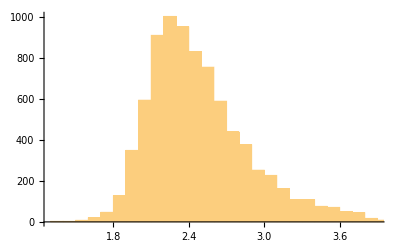

```mathematica
Histogram[MyEq[[2;;,12]]]
```

```mathematica
magnitudes=MyEq[[2;;,12]];
```

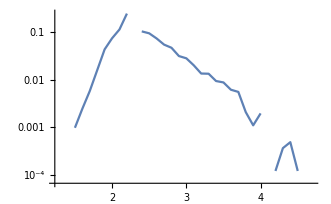

```mathematica
ListLogPlot[Transpose[{Range[1,6.,0.1],BinCounts[magnitudes,{1,6.1,0.1}]/Length[magnitudes]//N}],Joined->True,PlotRange->All]
```

```mathematica
(* LEt's focus on the area of Woods COunty - in a radius of 50km from Waynoka OK *)
```

```mathematica
WPos= Entity["City", {"Waynoka", "Oklahoma", "UnitedStates"}]//GeoPosition
```

GeoPosition[{36.5846,-98.8785}]

```mathematica
EqW=AroundPosition[ MyEq,WPos,50];   (* Get EQ from the base catalog in the surroinding *)
listPos=GeoPosition[{#[[3]], #[[4]]}] & /@ EqW[[2;;]];
```

```mathematica
Show[GeoListPlot[listPos,GeoLabels->Automatic],GeoGraphics[GeoDisk[WPos,50000]],GeoListPlot[ GeoPosition[  Entity["City", {#, "Oklahoma", "UnitedStates"}]]& /@ {"Waynoka","Alva"},GeoLabels->True,PlotStyle->Green] ]
```

-Graphics-

```mathematica
(* NOw for plotting - just EQ of Mw > 2.5 *)
```

```mathematica
EqW3=AboveMagnitude[EqW,2.5];
listPos3=GeoPosition[{#[[3]], #[[4]]}] & /@ EqW3[[2;;]];
```

```mathematica
data = {GeoPosition[{#[[3]], #[[4]]}] ->  10^(#[[12]]) } & /@ EqW3[[2;;]];
```

```mathematica
Max[#[[12]]&/@ EqW3[[2;;]] ]
```

4.7

```mathematica
WPos
```

GeoPosition[{36.5846,-98.8785}]

```mathematica
(* GETTING SEISMO STATION AROUND WPos *)
```

```mathematica
distStat =QuantityMagnitude@GeoDistance[WPos, #]&/@OKNetwork[[2;;,{3,4}]]; (* in km*)
kselect=Position[distStat,_?(#≤ 50&)]//Flatten;
OKstations=OKNetwork[[kselect+1]]
OKstationsLoc=GeoPosition[#]& /@OKstations[[;;,{3,4}]];
distStat =QuantityMagnitude@GeoDistance[WPos, #]&/@GSOKNetwork[[2;;,{3,4}]]; (* in km*)
kselect=Position[distStat,_?(#≤ 50&)]//Flatten;
GSOKstations=GSOKNetwork[[kselect+1]];
GSOKstationsLoc=GeoPosition[#]& /@GSOKstations[[;;,{3,4}]];
```

{{NOKA,Waynoka,Oklahoma,USA,36.6347,-98.9319,IRISDMC},{U32A,Winter Ranch,Mooreland,Oklahoma,USA,36.3795,-99.0014,IRISDMC}}

```mathematica
(* STATIONS worth of interests *)
GSOKstations[[;;,{1,2}]]//TableForm
```

OK035 |  E0210 Rd and N2420 Rd,Alva Oklahoma,USA
OK036 |  E0350 Rd betw N2450 and N2460,Cleo Springs,OK,USA
OK037 |  N2390 and E0350 Rds,Waynoka,OK,USA
OK038 |  West end E0370 Rd,Waynoka,OK USA
OK039 |  N2440 and E0440 Rds,Cleo Springs,OK,USA
OK040 |  E2430 and Blaine Rds,Waynoka,OK,USA
OK041 |  County Line and E0380 Rds,Cleo Springs,OK,USA
OK042 |  N2343 and E0420 Rds,Waynoka,OK,USA
OK043 |  N2390 and E0400 Rds,Waynoka,OK,USA
OKR1 |  West end E0370 Rd,Waynoka,OK rotational sensor

```mathematica
(* don t use the Rotational sensor *)
```

```mathematica
OKstations[[;;,{1,2}]]//TableForm
```

NOKA | Waynoka,Oklahoma,USA
U32A | Winter Ranch,Mooreland,Oklahoma,USA

```mathematica
(* 50km around Waynoka - stations in blue, towns in green,  EQ with dots representing magnitude from the EQ catalog *)
```

```mathematica
Show[GeoBubbleChart[data], GeoListPlot[OKstationsLoc,PlotStyle->Blue,PlotMarkers->GeoMarker],GeoListPlot[GSOKstationsLoc,PlotStyle->Blue,PlotMarkers->GeoMarker],GeoGraphics[GeoDisk[WPos,50000]],GeoListPlot[ GeoPosition[  Entity["City", {#, "Oklahoma", "UnitedStates"}]]& /@ {"Waynoka","Alva"},GeoLabels->True,PlotStyle->Green] ]
```

-Graphics-